/home/miguel_bengala/Documentos/SampleCode/Schroedinger

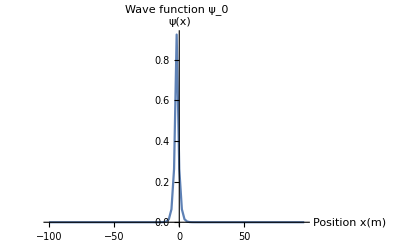

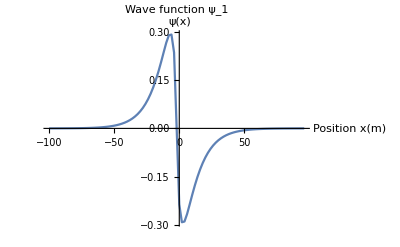

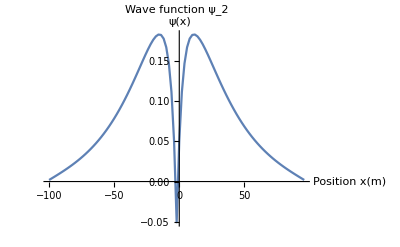

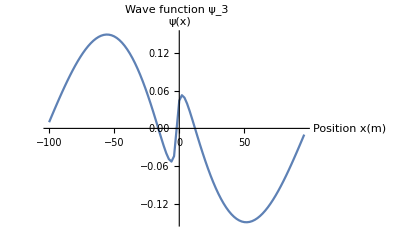

```mathematica
SetDirectory[NotebookDirectory[]]
Dados=Import["OutputWaves.txt",{"Table"}];
Dados0=Select[Dados,#[[1]]==0&];
fig0=ListLinePlot[Dados0[[All,{2,3}]],PlotLabel->"Wave function ψ_0",AxesLabel->{HoldForm[Position x[m]],HoldForm[ψ[x]]},LabelStyle->{GrayLevel[0]},PlotRange->All]
Dados1=Select[Dados,#[[1]]==1&];
fig1=ListLinePlot[Dados1[[All,{2,3}]],PlotLabel->"Wave function ψ_1",AxesLabel->{HoldForm[Position x[m]],HoldForm[ψ[x]]},LabelStyle->{GrayLevel[0]},PlotRange->All]
Dados2=Select[Dados,#[[1]]==2&];
fig2=ListLinePlot[Dados2[[All,{2,3}]],PlotLabel->"Wave function ψ_2",AxesLabel->{HoldForm[Position x[m]],HoldForm[ψ[x]]},LabelStyle->{GrayLevel[0]},PlotRange->All]
Dados3=Select[Dados,#[[1]]==3&];
fig3=ListLinePlot[Dados3[[All,{2,3}]],PlotLabel->"Wave function ψ_3",AxesLabel->{HoldForm[Position x[m]],HoldForm[ψ[x]]},LabelStyle->{GrayLevel[0]},PlotRange->All]
```